```mathematica
obnd=50;
e0=5;
ILnum[α_,β_,γ_,δ_]:=NIntegrate[1/((e-α)^2+β^2) 1/((e-γ)^2+δ^2),{e,e0,Infinity}]
ILana[α_,β_,γ_,δ_]:=1/(((α-γ)^2+(β-δ)^2) ((α-γ)^2+(β+δ)^2)) (((α-γ)^2+δ^2-β^2)/β (Pi/2+ArcTan[α/β])+((α-γ)^2-δ^2+β^2)/δ (Pi/2+ArcTan[γ/δ])-Aa[α,γ]/2 Log[(α^2+β^2)/(γ^2+δ^2)])
```

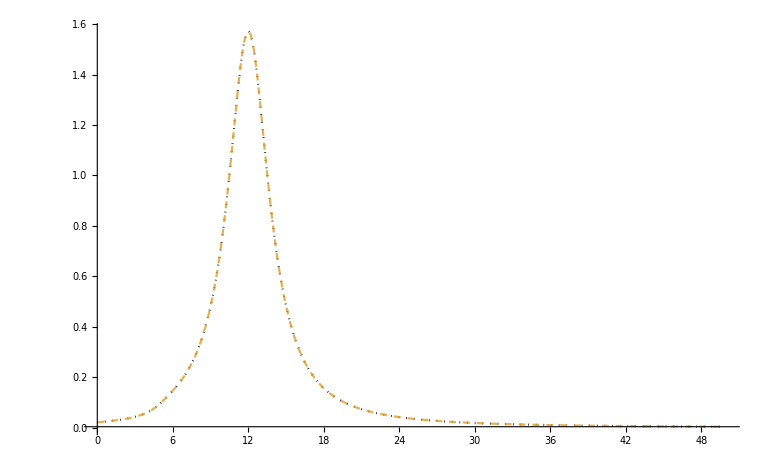

```mathematica
β=1.0;
γ=12.0;
δ=1.0;
Plot[{ILana[α-e0,β,γ-e0,δ],ILnum[α,β,γ,δ]},{α,0,obnd},PlotRange->Full,PlotStyle->{{Dotted,Black},{Dashed,Opacity[0.8]}}]
```